```mathematica
t=2;k=1;r=.05;g[t_,x_]:=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 1, "Expiration"->t},{"InterestRate"-> r, "Volatility" -> .25, "CurrentPrice"-> x, "Dividend"->0}]
h[t_,x_]:=FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 1, "Expiration"->t},{"InterestRate"-> r, "Volatility" -> .25, "CurrentPrice"-> x, "Dividend"->0}]
```

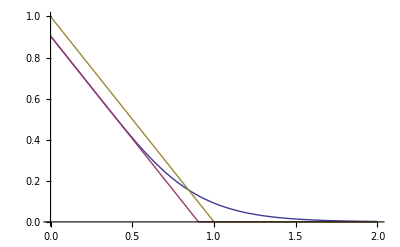

```mathematica
Plot[{g[t,x],Max[Exp[-t r]k-x,0],Max[k-x,0]},{x,0,2}]
```

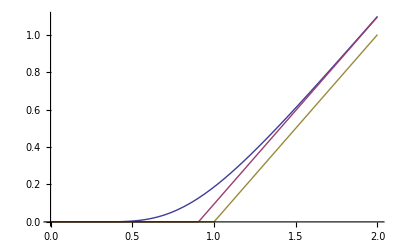

```mathematica
Plot[{h[t,x],Max[-Exp[-t r]k+x,0],Max[-k+x,0]},{x,0,2}]
```

```mathematica
dg[t_,x_]:=FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 1, "Expiration"->t},{"InterestRate"-> r, "Volatility" -> .25, "CurrentPrice"-> x, "Dividend"->0},{"Gamma"}]
```

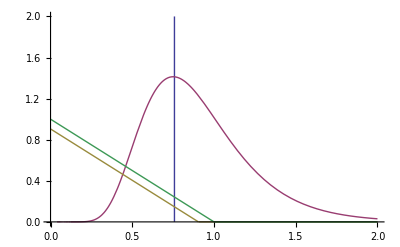

```mathematica
Plot[{100 Sign[x-Exp[-t r-σ √t/2]k],dg[t,x],Max[Exp[-t r]k-x,0],Max[k-x,0]},{x,0,2},PlotRange-> {0,2}]
```